# Reproduce Chen 2022 Calculation

```mathematica
Clear[m,s,Coul,kg]
u = 1.66053906660*10^-27 kg;
me = 9.1093837015*10^-31 kg;
c=299792458 m/s;
ϵ0 = 8.85418782 10^-12 (s^2 Coul^2)/(m^3 kg);
ℏ=6.62607004/(2π) 10^-34 (m^2 kg)/s;
kB = 1.3806485 10^-23 kg m^2/s^2 1/Kelvin;
μB=9.274009994*10^-28 kg m^2/s^2 1/G;
a0 = 5.29 10^-11 m;
electroncharge = 1.602 10^-19 Coul;
mSr = 1.46127 10^-25 kg; (*mass of 88Sr*)
cm = .01m;mm=10^-3 m;μm=10^-6 m;nm = 10^-9 m;
THz=10^12 s^-1;GHz=10^9 s^-1;MHz=10^6 s^-1;kHz=10^3 s^-1;
mW = 10^-3 kg m/s^2 m/s;W = kg m/s^2 m/s; μW=10^-6 W;
Tesla = 10000 G;
w0813 = .776μm;
M174plus = 173.938859*u - me;
M171plus = 170.936323*u - me;
R174= 109737.31568160 cm^-1 *M174plus/(M174plus+me);
R171= 109737.31568160 cm^-1 *M171plus/(M171plus+me);
ϵthr = 50443.07042 cm^-1;
Inuc = 1/2;
```

```mathematica
μ[n_, mus_] := mus[[1]] + mus[[2]]/(n-mus[[1]])^2+mus[[3]]/(n-mus[[1]])^4
Energy171[n_,mus_]:= (ϵthr -R171/(n-μ[n, mus])^2)
Energy174[n_,mus_]:= (ϵthr -R174/(n-μ[n, mus])^2)
```

## Quantum defect

```mathematica
rawQuantumDefect = Import[NotebookDirectory[]<>"Yb171QuantumDefect(Lehec+Thompson).csv"];
QuantumDefects = Association[StringJoin["μ's_",ToExpression[#[[1]]]]->ToExpression[{#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]]}]&/@ rawQuantumDefect ]
```

<|μ's_1S0→{4.27914,-5.625,91.65,-156050,-4.97×10^7,1.1×10^10},μ's_3S1→{4.4382,6,-18000.,0,0,0},μ's_1P1→{3.95433,-12.33,1729,0,0,0},μ's_1D2→{2.71309,-1.8646,-2145.5,3940500,-3.1×10^9,1.07×10^12},μ's_3D2→{2.74868,-0.52,-1186.01,1564600,-9.81×10^8,2.43×10^11}|>

For visual check try to calculate the energy level of 171Sr from this quantum defects data.

```mathematica
lvls1S0 = Table[{(ToString[n]<>"_1S0"),Energy174[n,QuantumDefects ["μ's_1S0"]]1/cm^-1},{n,6,100}];
lvls3S1 = Table[{(ToString[n]<>"_3S1"),Energy174[n,QuantumDefects ["μ's_3S1"]]1/cm^-1},{n,6,100}];
lvls1P1 = Table[{(ToString[n]<>"_1P1"),Energy174[n,QuantumDefects ["μ's_1P1"]]1/cm^-1},{n,6,100}];
lvls1D2 = Table[{(ToString[n]<>"_1D2"),Energy174[n,QuantumDefects ["μ's_1D2"]]1/cm^-1},{n,6,100}];
lvls3D2 = Table[{(ToString[n]<>"_3D2"),Energy174[n,QuantumDefects ["μ's_3D2"]]1/cm^-1},{n,6,100}];
```

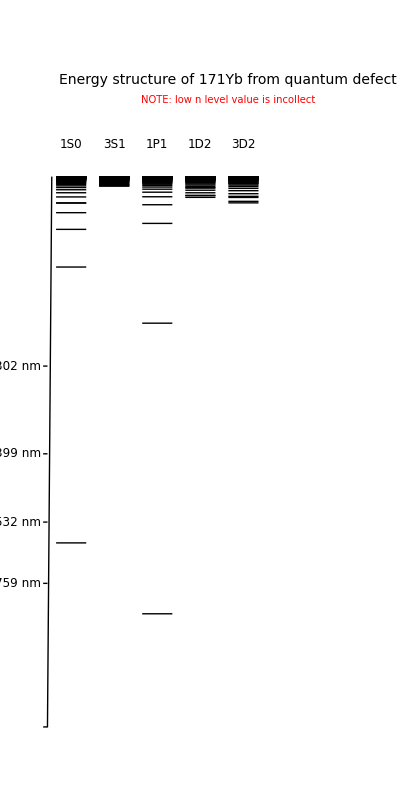

```mathematica
makeLevel[enlist_,J_]:=Line[{{J,#},{J+.7,#}}]&/@enlist[[;;,2]] ;
levelDiag = {makeLevel[lvls1S0,0],makeLevel[lvls3S1,1],makeLevel[lvls1P1,2],makeLevel[lvls1D2,3],makeLevel[lvls3D2,4]};
labellist={"1S0","3S1","1P1","1D2","3D2"};
levelLabels =Table[ {Black,Text[Style[labellist[[ii]],"Label",12],{0.35+ii-1,54000},{0,1}]},{ii,1,Length[labellist]}];
graphicLabel={{Black,Text[Style["Energy structure of 171Yb from quantum defect","Label",14],{4,60000},{0,1}]},
{Red,Text[Style["NOTE: low n level value is incollect","Label",10],{4,58000},{0,2}]}};
scaleinfo={ToString[#]<>" nm",(# nm)^-1 cm}&/@{759,532, 399, 302};
graphicScale={Line[{{-.3,0},{-.2,0},{-.1,50500 }}],Table[{Line[{{-.2,scaleinfo[[ii,2]]},{-.3,scaleinfo[[ii,2]]}}],Text[Style[scaleinfo[[ii,1]],12,"Label",Black],{-.35,scaleinfo[[ii,2]]},{1,0}]},{ii,1,Length[scaleinfo]}]};
levelGraphic=Graphics[{levelDiag ,graphicScale,levelLabels,graphicLabel},AspectRatio->2]
```

## Example calculation for 1S0, 3S1 n=60

```mathematica
μ1S0n82 = μ[60, QuantumDefects ["μ's_1S0"]];
μ3S1n82 = μ[60, QuantumDefects ["μ's_3S1"]];
```

```mathematica
Kin = DiagonalMatrix[Tan/@{π μ1S0n82,π μ3S1n82,π μ3S1n82}] ; Kin //MatrixForm
```

(1.18841 | 0. | 0.
0. | 5.0904 | 0.
0. | 0. | 5.0904)

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar) √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
```

```mathematica
Minout1 =DiagonalMatrix[{InOut1[0,0,0,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,3/2,3/2]}]; 
Kout1 = Transpose[Minout1].Kin.Minout1; Kout1 //MatrixForm
```

(1.18841 | 0. | 0.
0. | 5.0904 | 0.
0. | 0. | 5.0904)

```mathematica
Mout1out2 = {{Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 0],
Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 1],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 0],Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 1],
0},
{0,0,
Out1Out2[ 1/2, 1/2, 1, Inuc, 3/2, 1]}}; Mout1out2//MatrixForm
Kout2 = Transpose[Mout1out2].Kout1.Mout1out2;Kout2//MatrixForm
```

(-1/2 | (√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1)

(4.1149 | 1.68961 | 0.
1.68961 | 2.16391 | 0.
0. | 0. | 5.0904)

```mathematica
K = Kout2[[;;2,;;2]]; K//MatrixForm
```

(4.1149 | 1.68961
1.68961 | 2.16391)

## Find the Solution using the K matrix

```mathematica
Tanpiν2[Eb_] = FullSimplify[DiagonalMatrix[Tan[π √(R171/(# - Eb cm^-1)) ]&/@{-9.482109*0.033357 cm^-1,3.16073*0.033357 cm^-1,3.16073*0.033357 cm^-1}]]
Tanpiν[Eb_] = FullSimplify[DiagonalMatrix[Tan[π √(R171/(# - Eb cm^-1)) ]&/@{-9.482109*0.033357 cm^-1,3.16073*0.033357 cm^-1}]]
```

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.,0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))],0.},{0.,0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

```mathematica
Det[K + Tanpiν[Eb]]
```

6.0495+4.1149 Tan[1040.7 √(1/(0.105432-1. Eb))]+2.16391 Tan[1040.7 √(-1/(0.316295+1. Eb))]+Tan[1040.7 √(1/(0.105432-1. Eb))] Tan[1040.7 √(-1/(0.316295+1. Eb))]

```mathematica
ν1=(1.5298026328198352*^9 ν0)/(√(2.3402960953824993*^18-8.993910004533*^12 ν0^2))
```

(1.5298×10^9 ν0)/(√(2.3403×10^18-8.99391×10^12 ν0^2))

```mathematica
Det[K + DiagonalMatrix[Tan[π #] &/@{-ν0, ν1 }]]
```

6.0495-2.16391 Tan[π ν0]+4.1149 Tan[(4.80602×10^9 ν0)/(√(2.3403×10^18-8.99391×10^12 ν0^2))]-Tan[π ν0] Tan[(4.80602×10^9 ν0)/(√(2.3403×10^18-8.99391×10^12 ν0^2))]

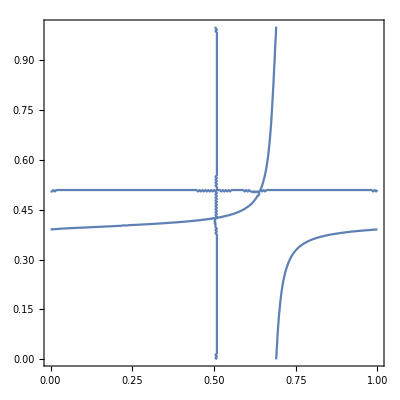

```mathematica
Clear[ν1,ν0]
ContourPlot[Det[K + DiagonalMatrix[Tan[π #] &/@{-ν0, ν1 }]]==0 ,{ν1, 0,1},{ν0, 0,1}]
```

```mathematica
Show[%381,FrameLabel->{{HoldForm[-ν0],None},{HoldForm[ν1],None}},PlotLabel->HoldForm[Lu-Fano plots (Chen2022 Fig. S1 a)],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%381,FrameLabel→{{-ν0,None},{ν1,None}},PlotLabel→Lu-Fano plots (Chen2022 Fig.S1 a),LabelStyle→{GrayLevel[0]}]

### Using 2*2 matrix

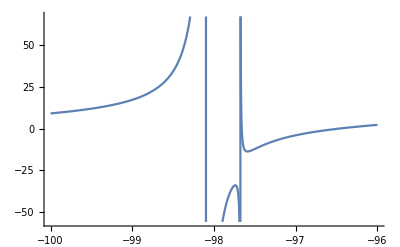

```mathematica
Plot[Det[K + Tanpiν[Eb]]== -0.00, {Eb, -100,-96}]
```

```mathematica
EnergyListrawA=  Solve[{Det[K + Tanpiν[Eb]]== 0, -10000000<Eb<-100},{Eb},Reals] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  Solve[{Det[K+ Tanpiν[Eb]]== 0, -100<Eb<-70},{Eb},Reals] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[K + Tanpiν[Eb]]== 0, -70<Eb<-50},{Eb},Reals] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[K + Tanpiν[Eb]]== 0, -50<Eb<-30},{Eb},Reals] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[K + Tanpiν[Eb]]== 0, -30<Eb<-20},{Eb},Reals] ;
EnergyListE = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[K + Tanpiν[Eb]]== 0, -20<Eb<-10},{Eb},Reals] ;
EnergyListF = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-347756.,-210127.,-44991.9,-36978.8,-16721.9,-14803.5,-8650.43,-7918.55,-5273.61,-4920.16,-3547.78,-3350.86,-2548.88,-2428.12,-1919.36,-1840.,-1497.23,-1442.3,-1200.48,-1160.87,-983.955,-954.437,-821.142,-798.546,-695.642,-677.947,-596.866,-582.74,-517.732,-506.265,-453.358,-443.913,-400.289,-392.408,-356.025,-349.373,-318.721,-313.048,-286.99,-282.106,-259.775,-255.535,-236.259,-232.547,-215.8,-212.528,-197.89,-194.986,-182.123,-179.529,-168.171,-165.839,-155.765,-153.657,-144.684,-142.769,-134.747,-132.998,-125.802,-124.197,-117.721,-116.24,-110.395,-109.024,-103.735,-102.46,-97.6605,-96.4699,-92.1063,-90.99,-87.0141,-85.9637,-82.3342,-81.3422,-78.0232,-77.0832,-74.0434,-73.1497,-70.3617,-69.5094,-66.9491,-66.1339,-63.7799,-62.998,-60.8315,-60.0797,-58.084,-57.3592,-55.5195,-54.819,-53.122,-52.4436,-50.8774,-50.2191,-48.7729,-48.1328,-46.7972,-46.1736,-44.9399,-44.3314,-43.1918,-42.597,-41.5444,-40.9622,-39.9901,-39.4195,-38.5221,-37.9622,-37.1342,-36.584,-35.8205,-35.2793,-34.5758,-34.043,-33.3955,-32.8704,-32.2751,-31.7572,-31.2107,-30.6994,-30.1985,-29.6935,-29.2353,-28.7361,-28.3178,-27.8242,-27.4433,-26.9549,-26.609,-26.1256,-25.8126,-25.334,-25.0518,-24.5777,-24.3244,-23.8548,-23.6285,-23.1633,-22.9623,-22.5015,-22.3241,-21.8678,-21.7123,-21.2607,-21.1253,-20.6788,-20.5617,-20.1209,-20.0201,-19.586,-19.4993,-19.0731,-18.9977,-18.5815,-18.514,-18.1104,-18.047,-17.6589,-17.5957,-17.226,-17.1596,-16.8102,-16.7381,-16.4105,-16.331,-16.0257,-15.9379,-15.6549,-15.5584,-15.2974,-15.1919,-14.9524,-14.838,-14.6193,-14.4961,-14.2975,-14.1657,-13.9864,-13.8464,-13.6857,-13.5377,-13.3948,-13.2391,-13.1132,-12.9503,-12.8406,-12.6708,-12.5765,-12.4004,-12.3206,-12.1386,-12.0723,-11.8854,-11.8314,-11.6405,-11.5971,-11.4041,-11.3689,-11.1765,-11.1458,-10.958,-10.927,-10.748,-10.7125,-10.5455,-10.5029,-10.3494,-10.2987,-10.1593,-10.1}

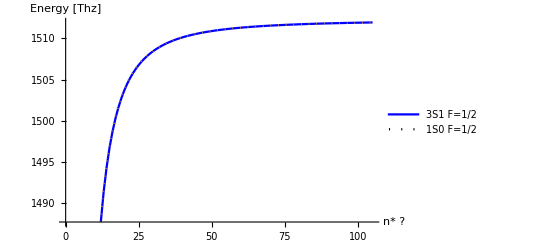

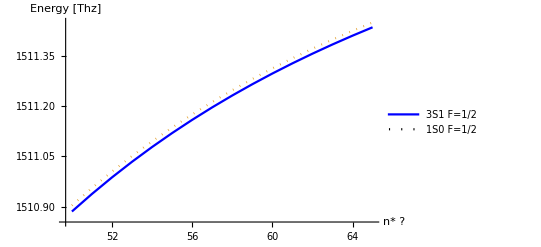

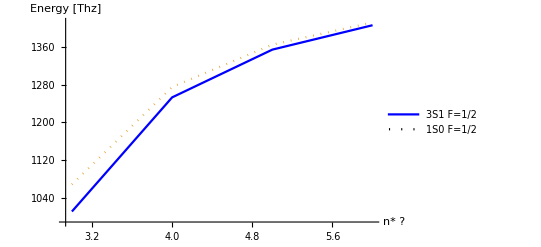

```mathematica
EnergyList2 = EnergyList  + ϵthr cm ;
EnergyList3 = Partition[EnergyList2,2]*29.979000*10^-3 ;
ListLinePlot[{EnergyList3[[;;,1]],EnergyList3[[;;,2]]},PlotStyle->{Blue,Dotted},PlotLegends->LineLegend[{Blue,Dotted},{"3S1 F=1/2","1S0 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[50;;65,1]],EnergyList3[[50;;65,2]]},PlotStyle->{Blue,Dotted},PlotLegends->LineLegend[{Blue,Dotted},{"3S1 F=1/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{50,65},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[3;;6,1]],EnergyList3[[3;;6,2]]},PlotStyle->{Blue,Dotted},PlotLegends->LineLegend[{Blue,Dotted},{"3S1 F=1/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{3,6},AxesLabel->{"
n* ?","Energy [Thz]"}]
```

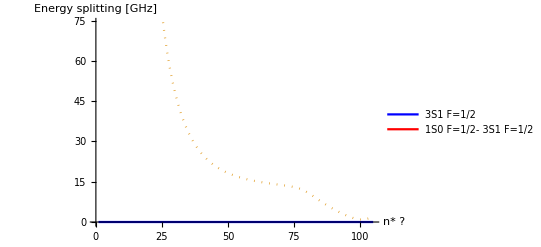

```mathematica
ListLinePlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{Blue,Dotted},PlotLegends->LineLegend[{Blue,Red,Dotted},{"3S1 F=1/2","1S0 F=1/2- 3S1 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

### USing 3*3 matrix

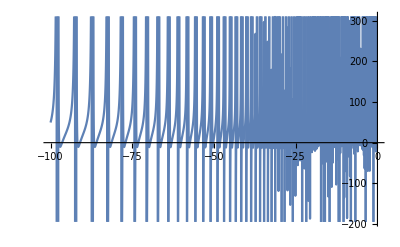

```mathematica
Plot[Det[Kout2 + Tanpiν2[Eb]]== -0.00, {Eb, -100,-0}]
```

```mathematica
EnergyListrawA=  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -10000000<Eb<-100},{Eb},Reals] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -100<Eb<-50},{Eb},Reals] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -50<Eb<-30},{Eb},Reals] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -30<Eb<-20},{Eb},Reals] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -20<Eb<-10},{Eb},Reals] ;
EnergyListE = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE]
```

{-347756.,-347756.,-210127.,-44991.9,-44991.6,-36978.8,-16721.9,-16721.6,-14803.5,-8650.43,-8650.12,-7918.55,-5273.61,-5273.3,-4920.16,-3547.78,-3547.46,-3350.86,-2548.88,-2548.57,-2428.12,-1919.36,-1919.04,-1840.,-1497.23,-1496.92,-1442.3,-1200.48,-1200.16,-1160.87,-983.955,-983.637,-954.437,-821.142,-820.825,-798.546,-695.642,-695.324,-677.947,-596.866,-596.548,-582.74,-517.732,-517.413,-506.265,-453.358,-453.039,-443.913,-400.289,-399.969,-392.408,-356.025,-355.704,-349.373,-318.721,-318.399,-313.048,-286.99,-286.667,-282.106,-259.775,-259.452,-255.535,-236.259,-235.934,-232.547,-215.8,-215.474,-212.528,-197.89,-197.563,-194.986,-182.123,-181.795,-179.529,-168.171,-167.841,-165.839,-155.765,-155.434,-153.657,-144.684,-144.352,-142.769,-134.747,-134.414,-132.998,-125.802,-125.467,-124.197,-117.721,-117.383,-116.24,-110.395,-110.056,-109.024,-103.735,-103.394,-102.46,-97.6605,-97.3181,-96.4699,-92.1063,-91.762,-90.99,-87.0141,-86.668,-85.9637,-82.3342,-81.9862,-81.3422,-78.0232,-77.6734,-77.0832,-74.0434,-73.6917,-73.1497,-70.3617,-70.0081,-69.5094,-66.9491,-66.5936,-66.1339,-63.7799,-63.4226,-62.998,-60.8315,-60.4724,-60.0797,-58.084,-57.7231,-57.3592,-55.5195,-55.1568,-54.819,-53.122,-52.7576,-52.4436,-50.8774,-50.5113,-50.2191,-48.7729,-48.4052,-48.1328,-46.7972,-46.4279,-46.1736,-44.9399,-44.5691,-44.3314,-43.1918,-42.8194,-42.597,-41.5444,-41.1706,-40.9622,-39.9901,-39.6149,-39.4195,-38.5221,-38.1456,-37.9622,-37.1342,-36.7564,-36.584,-35.8205,-35.4414,-35.2793,-34.5758,-34.1956,-34.043,-33.3955,-33.0142,-32.8704,-32.2751,-31.8927,-31.7572,-31.2107,-30.8273,-30.6994,-30.1985,-29.8142,-29.6935,-29.2353,-28.8501,-28.7361,-28.3178,-27.9318,-27.8242,-27.4433,-27.0565,-26.9549,-26.609,-26.2216,-26.1256,-25.8126,-25.4246,-25.334,-25.0518,-24.6633,-24.5777,-24.3244,-23.9355,-23.8548,-23.6285,-23.2393,-23.1633,-22.9623,-22.5729,-22.5015,-22.3241,-21.9347,-21.8678,-21.7123,-21.323,-21.2607,-21.1253,-20.7365,-20.6788,-20.5617,-20.1737,-20.1209,-20.0201,-19.6334,-19.586,-19.4993,-19.1144,-19.0731,-18.9977,-18.6156,-18.5815,-18.514,-18.136,-18.1104,-18.047,-17.6745,-17.6589,-17.5957,-17.2304,-17.226,-17.1596,-16.8102,-16.8027,-16.7381,-16.4105,-16.3906,-16.331,-16.0257,-15.9934,-15.9379,-15.6549,-15.6104,-15.5584,-15.2974,-15.2409,-15.1919,-14.9524,-14.8843,-14.838,-14.6193,-14.54,-14.4961,-14.2975,-14.2074,-14.1657,-13.9864,-13.8859,-13.8464,-13.6857,-13.5753,-13.5377,-13.3948,-13.2748,-13.2391,-13.1132,-12.9841,-12.9503,-12.8406,-12.7028,-12.6708,-12.5765,-12.4305,-12.4004,-12.3206,-12.1668,-12.1386,-12.0723,-11.9113,-11.8854,-11.8314,-11.6637,-11.6405,-11.5971,-11.4236,-11.4041,-11.3689,-11.1909,-11.1765,-11.1458,-10.9651,-10.958,-10.927,-10.748,-10.746,-10.7125,-10.5455,-10.5334,-10.5029,-10.3494,-10.3269,-10.2987,-10.1593,-10.1264,-10.1}

```mathematica
EnergyList2 = EnergyList  + ϵthr cm ;
EnergyList3 = Partition[EnergyList2,3]*29.979000*10^-3 ;
```

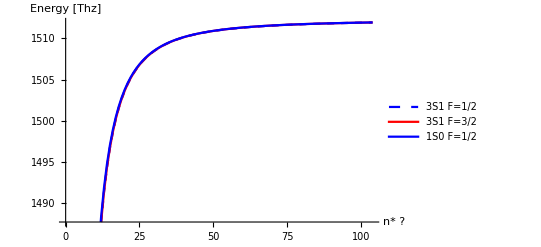

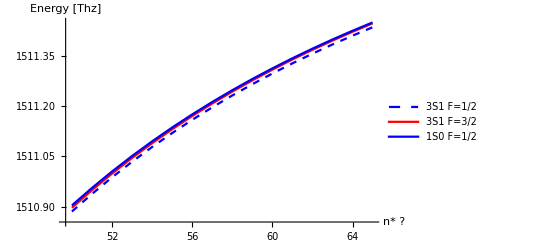

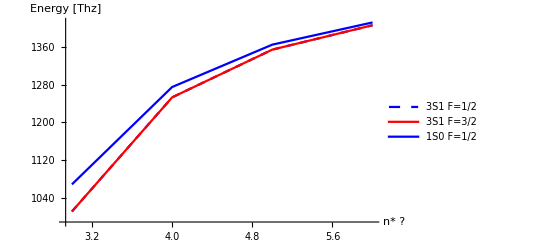

```mathematica
ListLinePlot[{EnergyList3[[;;,1]],EnergyList3[[;;,2]],EnergyList3[[;;,3]]},PlotStyle->{{Dashed,Blue},Red,Blue},PlotLegends->LineLegend[{{Dashed,Blue},Red,Blue},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[50;;65,1]],EnergyList3[[50;;65,2]],EnergyList3[[50;;65,3]]},PlotStyle->{{Dashed,Blue},Red,Blue},PlotLegends->LineLegend[{{Dashed,Blue},Red,Blue},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{50,65},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListLinePlot[{EnergyList3[[3;;6,1]],EnergyList3[[3;;6,2]],EnergyList3[[3;;6,3]]},PlotStyle->{{Dashed,Blue},Red,Blue},PlotLegends->LineLegend[{{Dashed,Blue},Red,Blue},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{3,6},AxesLabel->{"
n* ?","Energy [Thz]"}]
```

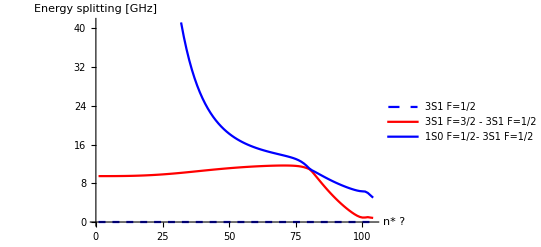

```mathematica
ListLinePlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{{Dashed,Blue},Red,Blue},PlotLegends->LineLegend[{{Dashed,Blue},Red, Blue},{"3S1 F=1/2","3S1 F=3/2 - 3S1 F=1/2","1S0 F=1/2- 3S1 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

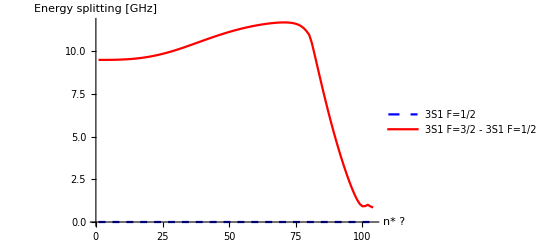

```mathematica
ListLinePlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{{Dashed,Blue},Red},PlotLegends->LineLegend[{{Dashed,Blue},Red},{"3S1 F=1/2","3S1 F=3/2 - 3S1 F=1/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

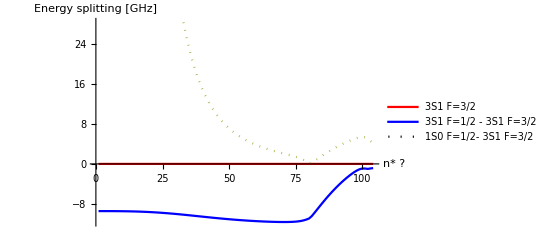

```mathematica
ListLinePlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,1]]-EnergyList3[[;;,2]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,2]])*10^3},PlotStyle->{Red,Blue,Dotted},PlotLegends->LineLegend[{Red,Blue,Dotted},{"3S1 F=3/2","3S1 F=1/2 - 3S1 F=3/2","1S0 F=1/2- 3S1 F=3/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

```mathematica
"interactive plot"%399DynamicModule[{xc,dx},Manipulate[Plot[Det[K+Tanpiν[Eb]]==0,{Eb,xc-dx,xc+dx}],{{xc,-99/2,"center"},-705/2,507/2},{{dx,50.5,"zoom"},303,3.0300000000000002}],DynamicModuleValues:>{}]
```

### Energy dependent quantum defect

```mathematica
Clear[η,μenergy,Kout]
```

```mathematica
rawQuantumDefect = Import[NotebookDirectory[]<>"Yb171QuantumDefect(ARC+Thompson).csv"];
QuantumDefects = Association[StringJoin["μ's_",ToExpression[#[[1]]]]->ToExpression[{#[[2]],#[[3]],#[[4]]}]&/@ rawQuantumDefect ]
```

<|μ's_1S0→{4.27837,-5.60943,-258.5},μ's_3S1→{4.4382,6,-18000.},μ's_1P1→{3.95343,-10.5829,728.1},μ's_1D2→{2.71301,-0.929878,-636.4},μ's_3D2→{2.7486,0.0137,-106.55}|>

```mathematica
FullSimplify[DiagonalMatrix[Tan[π √(R171/(# - Eb cm^-1)) ]&/@{-9.482109*0.033357 cm^-1,3.16073*0.033357 cm^-1,3.16073*0.033357 cm^-1}]]
```

{{Tan[1040.7 √(-1/(0.316295+1. Eb))],0.,0.},{0.,Tan[1040.7 √(1/(0.105432-1. Eb))],0.},{0.,0.,Tan[1040.7 √(1/(0.105432-1. Eb))]}}

```mathematica
Tanpiν2[Eb_] := {{Tan[1040.7018871781286 √(-1/(0.31629470991299996+1. Eb))],0.,0.},{0.,Tan[1040.7018871781286 √(1/(0.10543247061-1. Eb))],0.},{0.,0.,Tan[1040.7018871781286 √(1/(0.10543247061-1. Eb))]}}
```

```mathematica
R171nonUnit = R171/cm^-1;
η[Eb_]:= -Eb /R171nonUnit ;
μenergy[Eb_, mus_]:=mus[[1]]+ η[Eb]^1 mus[[2]]+η[Eb]^2 mus[[3]];
```

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar) √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
Minout1 =DiagonalMatrix[{InOut1[0,0,0,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,1/2,1/2],InOut1[1,0,1,Inuc,3/2,3/2]}]; 
Mout1out2 = {{Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 0],
Out1Out2[ 1/2, 1/2, 0, Inuc, 1/2, 1],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 0],Out1Out2[ 1/2, 1/2, 1, Inuc, 1/2, 1],
0},
{0,0,
Out1Out2[ 1/2, 1/2, 1, Inuc, 3/2, 1]}};
Kout[Eb_]:= Transpose[Mout1out2].Transpose[Minout1].DiagonalMatrix[Tan/@{π μenergy[Eb,QuantumDefects ["μ's_1S0"]],π μenergy[Eb,QuantumDefects ["μ's_3S1"]],π μenergy[Eb,QuantumDefects ["μ's_3S1"]]}] .Minout1.Mout1out2
```

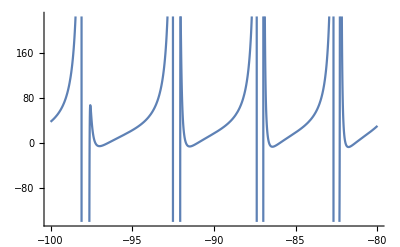

```mathematica
Plot[Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, {Eb, -100,-80}]
```

```mathematica
EnergyListrawZ=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -1000000<Eb<-5000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListZ= Eb/.EnergyListrawZ;
EnergyListrawA=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -5000<Eb<-1000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -1000<Eb<-500},{Eb},Reals, WorkingPrecision->10] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -500<Eb<-100},{Eb},Reals, WorkingPrecision->10] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0, -100<Eb<-50},{Eb},Reals, WorkingPrecision->10] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -50<Eb<-30},{Eb},Reals, WorkingPrecision->10] ;
EnergyListE = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -30<Eb<-15},{Eb},Reals, WorkingPrecision->10] ;
EnergyListF = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -15<Eb<-10},{Eb},Reals, WorkingPrecision->10] ;
EnergyListG = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListZ,EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-9445.7104105137375565,-9445.7083985807350089,-9410.3888130772038702,-9410.3867823057783815,-9374.9360224759090656,-9374.9339725487105713,-9339.3505782655132669,-9339.3485088571702224,-9303.6309928721121486870272,-9303.628903649022672,-9267.7757508851092992,-9267.7736415052088445,-9231.78330832631968058,-9231.7811784388285833,-9195.6520918943263857,-9195.6499411394791481,-9159.3804981830645341,-9159.378326191821755,-9122.9668928735553131,-9122.96469926729848626,-9086.40960989765958368,-9086.4073942878684567,-9049.7069505726639074,-9049.7047125605756237,-9012.8571827054520929,-9012.8549218817008545,-8975.8585396649521893856,-8975.8562556091876123,-8863.9511562065607238,-8863.948799816554878119,-8826.3386230439084151,-8826.3362416220851174,-8788.567830118635481,-8788.5654231829940354,-8750.6367827340239302,-8750.6343497885814173,-8712.5434442491765656,-8712.5409847832370402,-8674.285734841664888,-8674.28324832893263204,-8635.8615302232045951,-8635.8590161206413499,-8597.2686603062610069,-8597.2661180524895282685,-8558.50490781949322802,-8558.5023368323240657,-8519.56800687017019399,-8519.565406542249662,-8480.4556414526836608,-8480.4530111425526298,-8441.1654439065448605,-8441.162782916281571057,-8401.6949933503937936,-8401.69230085159916029,-8362.0418143322730012,-8362.0390889588529118,-8322.20339536523720433,-8322.2006145191353335,-8318.201983848122900026,-8282.177072116981018,-8282.1742862609144565,-8241.9602736756008725,-8241.9574524611134551681945,-8201.5502552597385507,-8201.54739896680195332925,-8160.94423903594874831,-8160.9413471334305562,-8120.13937988783334614,-8120.1364516752930051,-8079.1327637189586295,-8079.12979842363582455,-8037.9214051848472096,-8037.9184019875520482,-7996.5022452686329719,-7996.499203312492050345,-7954.87214873732636212,-7954.8690671308990304,-7913.0279014809929942,-7913.0247792991274937,-7870.966207730796132155,-7870.9630440144281864529,-7828.6836871499942705,-7828.6804809053802252,-7786.1768717911118249,-7786.1736219887182645478,-7743.442202911880137297,-7743.43890848503690933,-7700.4760276419834189,-7700.472687485353376,-7657.2745954920778455,-7657.2712084599695705,-7613.8340546959578407,-7613.8306196004928858,-7570.1504483761099817,-7570.1469639852474224,-7526.2197105222145939,-7526.2161755576299219,-7482.0376617714220282,-7482.0340749062329775,-7437.6000049784392997,-7437.59636483476712944,-7392.9023205626075667,-7392.8986257089577992,-7347.9400616182259535591,-7347.9363105666666895,-7302.7085487733763093,-7302.7047399764836383,-7257.2029647814203617,-7257.1990966289466579,-7211.4183488281695464,-7211.4144196433669338,-7165.3495905364646185,-7165.34559857195293478,-7118.9914236485488897,-7118.9873670815336095,-7072.3384193651946051,-7072.33429629166389698,-7025.3849793191182204,-7025.3807877462442861,-6978.1253281590468537,-6978.1210659939863502,-6930.5535057208227007,-6930.5491707510930091,-6882.6633587674740516,-6882.658948617378942324,-6834.44853231785124347819,-6834.4440443147144207,-6785.902460936881151479,-6785.8978914141139863,-6737.0183836738485802,-6737.0137025149866301,-6730.1691790930190641,-6687.7891857687441806,-6687.7844588369903786,-6638.2077166651402333,-6638.2028991815624215,-6588.2664171377347232,-6588.2615082164934939,-6537.957507012064269,-6537.9525040328456632,-6487.2729250103970471,-6487.2678249190349507,-6436.2043158011041889,-6436.1991152919683235,-6384.74301516227116166596,-6384.7377107196867242,-6332.8800340583604947,-6332.8746219639637188,-6280.6060416362743168,-6280.6005179646773586,-6227.9113470712570872,-6227.9057076804369509,-6174.7858801732104837,-6174.7801206918230324,-6121.2191706521566044,-6121.2132864645935344,-6067.2003259307447197,-6067.1943121602151593,-6012.7180073803000865,-6012.7118588699755691,-5957.7604048444533969,-5957.7541161365823346,-5902.3152093005993382,-5902.3087746134037449,-5846.3695834941011124,-5846.3629966961788569,-5789.9101303630785526,-5789.9033849449203846,-5732.9228590525777772,-5732.9159480946282699,-5675.3931482957093454,-5675.3860644320678125,-5617.3057069157998983,-5617.2984422919535867,-5558.64453117780451,-5558.6370773990898596,-5499.3928586902369264,-5499.385206752977261411528,-5439.5331185364686916,-5439.5252587176829014,-5379.046877331553473,-5379.0387989419120006,-5317.9147812898926739,-5317.9064716916793179,-5256.1165069798619888,-5256.1079361301599714,-5236.3044071208673178,-5193.6305791738351843,-5193.6217970255353961,-5130.43458522664764048,-5130.4255293072043897,-5066.5047342381713392,-5066.4953958227951382,-5001.8159931024453183,-5001.8063575721215478,-4936.3419248416292951,-4936.3319756086557797,-4870.0545848475009572,-4870.0443037032939487,-4802.9244036774105686,-4802.9137707582491569,-4734.9200581885685755,-4734.9090518399838673,-4666.00832997758833652045,-4665.9969265685678621,-4596.15394975897267917,-4596.1421234564788225,-4525.3194261300700376,-4525.3071486330642867,-4453.464856996244116,-4453.4520972231331089,-4380.5477217543355037,-4380.5344454725938363,-4306.5226521594556703,-4306.508821536453343,-4231.3411796482457572,-4231.3267526745474105,-4154.9514568298247044,-4154.9363864538374201,-4077.2979513723921101,-4077.2821834578227127,-3998.3211239734711253,-3998.3045789921679311,-3963.9271230901473371,-3917.9569029606551806,-3917.9396114103073096,-3836.13671161950688849,-3836.1185150540615664,-3752.7864451340431384,-3752.7672765498675975,-3667.8263851086501723,-3667.8061545302552613,-3581.1705618760210312,-3581.1491650805972641,-3492.726221539625612,-3492.7035388266936365,-3402.393267728171152,-3402.3691613173641505,-3310.0637068367559532,-3310.0380173466197669,-3215.6211321588831966,-3215.5936738336350714,-3118.9403047419379742,-3118.9108574987807623,-3019.886954039364735,-3019.855216943901133103,-2983.1157657109497228,-2918.3175523908363674,-2918.28341018883374,-2814.0807907373009449,-2814.0437379540678785,-2707.0180296052365925,-2706.9776648414268703,-2596.9669390277279021,-2596.9227573292063949,-2483.7664667020573676,-2483.717851649791269,-2367.2655070458268301,-2367.2116908605769566,-2272.7279531585293676,-2247.3365056297219167,-2247.2768931448020397,-2123.8989642079083445,-2123.8319792264220876,-1996.9508292810147627,-1996.8752772201778418,-1866.6213902983496777,-1866.5356038817552574,-1767.6791733462900982,-1733.2424551709028151,-1733.1449068212104316,-1597.4477720227261846,-1597.3356071328414091,-1460.2856777891727295,-1460.1564720236979881,-1405.5692383461822795,-1323.3287040568699592,-1323.1805954333561673,-1188.7168280872656082,-1188.5469703755543652,-1140.7813118290057575,-1059.0424906731988181,-1058.8505768809626948,-942.75787119526013191,-937.03013730196414081,-936.81963798365158684,-825.06583753703081918,-824.8300788002417872,-791.39206731373873125,-724.70345745386831235,-724.45002852172757778,-673.37636302306575723,-636.49858563136168949,-636.23069240086459398,-579.71274510823240716,-560.08619740203442919,-559.80735559289158695,-504.1999169564027906,-494.4798966980104198,-494.19377824373652881,-442.4706449199001075,-438.39042547955646247,-438.10216748285022819,-391.40341403127711544,-390.45202764157997585,-390.18570589233510329,-349.52127548958763579,-349.18160477058310496,-348.57869839512061758,-314.30066168419713257,-313.97584102481999554,-312.46619241229914902,-283.94284157138368735,-283.61947564163553196,-281.66735351665073479,-257.64388705791488939,-257.32003804362732941,-255.19813584370703716,-234.74744847521915399,-234.4225871401292437,-232.28590084614215141,-214.71435083630498487,-214.38829046330869111,-212.3220073090955424,-197.10153953565973822,-196.77419615259292538,-194.82225017079689581,-181.54428556201792003,-181.21560664065550284,-179.39768062444964778,-167.74140514067302435,-167.41134596102128769,-165.73303848671288279,-155.44320553030239443,-155.11172153913049726,-153.57064903018591619,-144.44176130202372095,-144.10880632017459816,-142.6982689019763488,-134.56311333560473321,-134.22863994294989428,-132.93981643416452684,-125.6610217501381222,-125.32498241900891654,-124.14823195684063628,-117.61196042843563454,-117.2743088282960372,-116.19992777706434077,-110.31109788761214684,-109.97179012738885268,-108.99043651496268683,-103.66906006025050499,-103.32805577820125658,-102.43097137874180241,-97.609313065964415872,-97.26657633766586821,-96.445686601451803822,-92.066038457635981669,-91.721538518262973298,-90.969479945990704813,-86.982400746362591481,-86.636112534094661821,-85.946218189559005464,-82.3091284744703416,-81.961033006338955434,-81.327295112695690227,-78.003346878640795403,-77.6534314721930356,-77.070452701616434627,-74.027613261525311758,-73.675871616881521798,-73.138812091293100178,-70.349116383620715731,-69.995548541404997809,-69.500072686188115423,-66.939009143806719866,-66.583621335158105107,-66.125846931571183351,-63.771850041953279468,-63.414654447342443441,-62.99110511473021073,-60.825133801713553261,-60.466148235514913007,-60.073709891002751674,-58.078895377677742554,-57.71814291531626781,-57.35402434802791871,-55.515374610517113887,-55.15288317449913265,-54.814580632775993418,-53.118731205052878793,-52.754533125319366931,-52.439798684760108615,-50.874801626736744481,-50.508933189601550068,-50.215746606020705333,-48.770891047822312988,-48.403392046358018041,-48.129935774855905901,-46.795594707522947573,-46.426508004729622806,-46.171145067364618611,-44.938644044299738605,-44.568015158836860703,-44.329269558403980337,-43.190773762618489857,-42.818650485394315825,-42.595189884987437334,-41.543606649739108776,-41.170038698323187907,-40.960659111669476928,-39.989553490682178903,-39.614592207414293383,-39.418204471020686272,-38.521725865319988739,-38.145423964203919727,-37.961041787789166845,-37.133859969408120153,-36.756271336469826024,-36.583000752279373702,-35.8202498962418111,-35.441429448072727433,-35.27845950222402055,-34.57568905935910645,-34.195692665146841847,-34.042287215149906216,-33.395418638781697083,-33.014303112375530639,-32.869793614641847091,-32.275082101239316533,-31.892905271885030791,-31.756684461771499854,-31.210684984698180632,-30.827505858272884015,-30.699022243581685269,-30.198559254111467592,-29.814438281400149071,-29.693191389077048219,-29.23533163241599322,-28.850331107821252204,-28.73586744401541121,-28.317895391324349327,-27.932080015356203762,-27.823989722714932643,-27.443385152510229429,-27.056822805980123483,-26.954737031619772448,-26.609154302637258821,-26.221917102085002088,-26.125506129119766411,-25.812754665656247067,-25.424920402039398446,-25.333892653301346349,-25.051918101920027138,-24.663572214299243643,-24.577674319471766736,-24.324539713045833282,-23.935778026317232137,-23.854796270568037569,-23.628662318169139765,-23.239594896161298093,-23.163358568484911146,-22.962461820551964094,-22.573218481916185403,-22.501605962262697691,-22.324232985615970426,-21.934971347298585957,-21.867920286867863428,-21.712374976724663499,-21.323292402043759318,-21.260816157714062111,-21.125375720756061442,-20.736727353003698339,-20.678940990551638458,-20.561793843126771687,-20.173920056939634953,-20.121080446804824223,-20.020236869286674688,-19.633604679036356359,-19.586168760191916269,-19.499336058091070701,-19.114598572500233993,-19.073295931054236032,-18.99772572287268698,-18.615795804470279348,-18.581684341709758729,-18.514054347462321111,-18.136161262077945156,-18.110587785190635095,-18.047074381372552662,-17.67472528001167174,-17.659117001737013571,-17.595806510375523846,-17.230578737525117418,-17.226140918786206713,-17.159629109674983925,-16.810392179382927657,-16.802868578600450278,-16.738164208581104912,-16.410653025674415033,-16.390793714048377263,-16.331083823545320748,-16.025853809904422238,-15.993601268787504057,-15.938004319368424788,-15.655077802601672281,-15.610583141476715204,-15.558475069083984834,-15.297531153371379824,-15.241072847143907162,-15.192002504841986468}

```mathematica
EnergyList = Join[EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF,EnergyListG];
EnergyList2 = EnergyList  + ϵthr cm ;
EnergyList3 = Partition[Delete[EnergyList2,{{1},{2}}],3]*29.979000*10^-3; NumberForm[EnergyList3 ,10]
```

{{1484.147892,1487.498159,1487.505227},{1488.507665,1490.506923,1490.514521},{1492.045658,1493.151217,1493.159248},{1494.8536,1495.441984,1495.450343},{1497.117399,1497.408795,1497.417373},{1498.967981,1499.090302,1499.098943},{1500.498925,1500.527447,1500.535431},{1501.75451,1501.764693,1501.782767},{1502.810389,1502.820126,1502.865384},{1503.720486,1503.73018,1503.788703},{1504.508902,1504.518611,1504.582223},{1505.195314,1505.205053,1505.269109},{1505.795887,1505.805662,1505.867607},{1506.323901,1506.333714,1506.392232},{1506.790292,1506.800145,1506.854645},{1507.204089,1507.213983,1507.264297},{1507.572776,1507.582714,1507.628914},{1507.902589,1507.91257,1507.954857},{1508.198741,1508.208768,1508.247405},{1508.465616,1508.47569,1508.510968},{1508.706919,1508.717042,1508.74925},{1508.925792,1508.935964,1508.965384},{1509.124913,1509.135136,1509.16203},{1509.306579,1509.316853,1509.341463},{1509.47276,1509.483088,1509.505634},{1509.625163,1509.635544,1509.656226},{1509.765263,1509.775698,1509.794697},{1509.894346,1509.904836,1509.922313},{1510.013534,1510.024079,1510.04018},{1510.123812,1510.134412,1510.149265},{1510.226044,1510.236698,1510.250421},{1510.320992,1510.3317,1510.344398},{1510.409331,1510.420093,1510.431858},{1510.491661,1510.502476,1510.513392},{1510.568513,1510.57938,1510.589522},{1510.640362,1510.65128,1510.660715},{1510.707632,1510.718601,1510.72739},{1510.770706,1510.781723,1510.789921},{1510.829923,1510.840988,1510.848643},{1510.885593,1510.896704,1510.903861},{1510.937992,1510.949148,1510.955847},{1510.987372,1510.998572,1511.004849},{1511.033961,1511.045202,1511.05109},{1511.077965,1511.089246,1511.094774},{1511.119572,1511.130892,1511.136086},{1511.158953,1511.17031,1511.175195},{1511.196264,1511.207655,1511.212254},{1511.231647,1511.243072,1511.247405},{1511.265233,1511.276691,1511.280774},{1511.297143,1511.30863,1511.312482},{1511.327486,1511.339001,1511.342636},{1511.356362,1511.367904,1511.371336},{1511.383866,1511.395432,1511.398673},{1511.410083,1511.421672,1511.424732},{1511.435092,1511.446701,1511.449592},{1511.458968,1511.470594,1511.473323},{1511.481777,1511.493419,1511.495994},{1511.503583,1511.515237,1511.517665},{1511.524444,1511.536108,1511.538394},{1511.544416,1511.556086,1511.558232},{1511.56355,1511.57522,1511.57723},{1511.581893,1511.593557,1511.59543},{1511.59949,1511.611142,1511.612874},{1511.616386,1511.628014,1511.629598},{1511.632621,1511.644212,1511.645634},{1511.648238,1511.659772,1511.66101},{1511.663275,1511.674725,1511.675748},{1511.677775,1511.689104,1511.689871},{1511.691775,1511.702938,1511.703405},{1511.705303,1511.716253,1511.716386},{1511.71838,1511.728849,1511.729075},{1511.731015,1511.740833,1511.741429},{1511.743219,1511.752369,1511.753336},{1511.755003,1511.763485,1511.764818},{1511.766381,1511.774203,1511.775896},{1511.777367,1511.784547,1511.786587},{1511.787977,1511.794533,1511.79691},{1511.798227,1511.804181,1511.806882},{1511.808131,1511.813505,1511.816517},{1511.817703,1511.822521,1511.825832},{1511.826958,1511.831243,1511.83484},{1511.835909,1511.839684,1511.843554},{1511.844568,1511.847857,1511.851987},{1511.852946,1511.855774,1511.860151},{1511.861054,1511.863447,1511.868058},{1511.868901,1511.870889,1511.875718},{1511.876494,1511.878113,1511.883141},{1511.883836,1511.885134,1511.890337},{1511.890923,1511.891976,1511.897315},{1511.897745,1511.898665,1511.904083},{1511.904295,1511.905226,1511.91059},{1511.910651,1511.911656,1511.916663},{1511.917026,1511.917938,1511.92254},{1511.923215,1511.92406,1511.928239}}

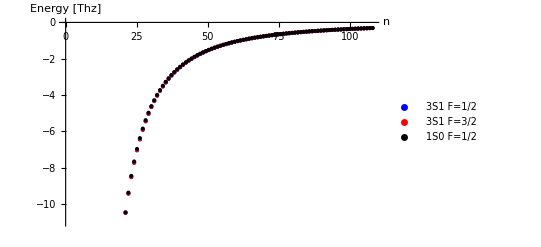

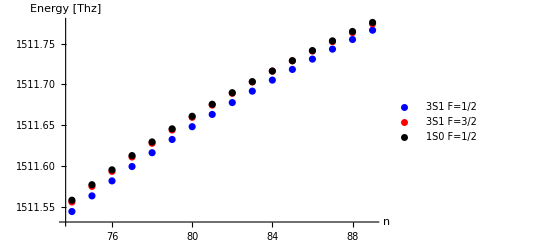

{{1511.544416,1511.556086,1511.558232},{1511.56355,1511.57522,1511.57723},{1511.581893,1511.593557,1511.59543},{1511.59949,1511.611142,1511.612874},{1511.616386,1511.628014,1511.629598},{1511.632621,1511.644212,1511.645634},{1511.648238,1511.659772,1511.66101},{1511.663275,1511.674725,1511.675748},{1511.677775,1511.689104,1511.689871},{1511.691775,1511.702938,1511.703405},{1511.705303,1511.716253,1511.716386},{1511.71838,1511.728849,1511.729075},{1511.731015,1511.740833,1511.741429},{1511.743219,1511.752369,1511.753336},{1511.755003,1511.763485,1511.764818},{1511.766381,1511.774203,1511.775896}}

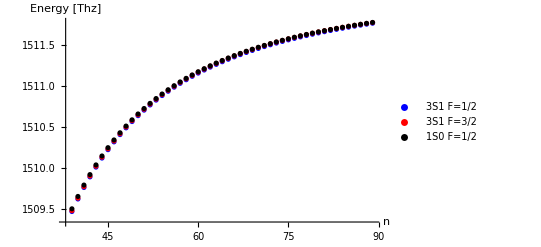

{{1510.123812,1510.134412,1510.149265},{1510.226044,1510.236698,1510.250421},{1510.320992,1510.3317,1510.344398},{1510.409331,1510.420093,1510.431858},{1510.491661,1510.502476,1510.513392},{1510.568513,1510.57938,1510.589522},{1510.640362,1510.65128,1510.660715},{1510.707632,1510.718601,1510.72739},{1510.770706,1510.781723,1510.789921},{1510.829923,1510.840988,1510.848643},{1510.885593,1510.896704,1510.903861},{1510.937992,1510.949148,1510.955847},{1510.987372,1510.998572,1511.004849},{1511.033961,1511.045202,1511.05109},{1511.077965,1511.089246,1511.094774},{1511.119572,1511.130892,1511.136086},{1511.158953,1511.17031,1511.175195},{1511.196264,1511.207655,1511.212254},{1511.231647,1511.243072,1511.247405},{1511.265233,1511.276691,1511.280774},{1511.297143,1511.30863,1511.312482},{1511.327486,1511.339001,1511.342636},{1511.356362,1511.367904,1511.371336},{1511.383866,1511.395432,1511.398673},{1511.410083,1511.421672,1511.424732},{1511.435092,1511.446701,1511.449592},{1511.458968,1511.470594,1511.473323},{1511.481777,1511.493419,1511.495994},{1511.503583,1511.515237,1511.517665},{1511.524444,1511.536108,1511.538394},{1511.544416,1511.556086,1511.558232},{1511.56355,1511.57522,1511.57723},{1511.581893,1511.593557,1511.59543},{1511.59949,1511.611142,1511.612874},{1511.616386,1511.628014,1511.629598},{1511.632621,1511.644212,1511.645634},{1511.648238,1511.659772,1511.66101},{1511.663275,1511.674725,1511.675748},{1511.677775,1511.689104,1511.689871},{1511.691775,1511.702938,1511.703405},{1511.705303,1511.716253,1511.716386},{1511.71838,1511.728849,1511.729075},{1511.731015,1511.740833,1511.741429},{1511.743219,1511.752369,1511.753336},{1511.755003,1511.763485,1511.764818},{1511.766381,1511.774203,1511.775896}}

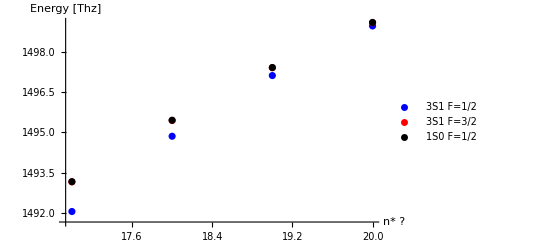

```mathematica
ListPlot[{EnergyList3[[;;,1]]-ϵthr  cm *29.979000*10^-3 ,EnergyList3[[;;,2]]-ϵthr  cm *29.979000*10^-3 ,EnergyList3[[;;,3]]-ϵthr  cm *29.979000*10^-3 },PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"}],AxesLabel->{"
n","Energy [Thz]"},DataRange->{14,Length[EnergyList3[[;;,1]]]+14}]
ListPlot[{EnergyList3[[60;;75,1]],EnergyList3[[60;;75,2]],EnergyList3[[60;;75,3]]},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{74,89},AxesLabel->{"
n","Energy [Thz]"}]
NumberForm[EnergyList3[[60;;75]] ,10]
ListPlot[{EnergyList3[[25;;75,1]],EnergyList3[[25;;75,2]],EnergyList3[[25;;75,3]]},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{39,89},AxesLabel->{"
n","Energy [Thz]"}]
NumberForm[EnergyList3[[30;;75]] ,10]
ListPlot[{EnergyList3[[3;;6,1]],EnergyList3[[3;;6,2]],EnergyList3[[3;;6,3]]},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{17,20},AxesLabel->{"
n* ?","Energy [Thz]"}]
```

### Convert this list to 976 IFDL out put value

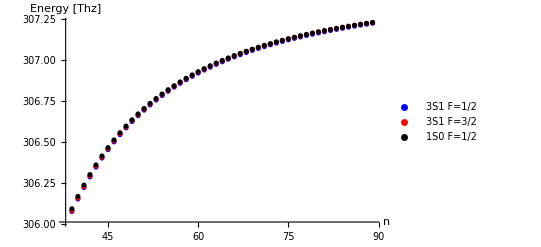

{{306.4010207,306.4063205,306.4137475},{306.4521365,306.4574636,306.4643254},{306.4996107,306.5049649,306.5113137},{306.5437805,306.5491615,306.555044},{306.5849452,306.5903527,306.5958107},{306.6233711,306.6288047,306.6338757},{306.6592956,306.6647548,306.6694725},{306.692931,306.6984152,306.7028099},{306.7244676,306.7299762,306.7340752},{306.7540763,306.7596087,306.7634364},{306.781911,306.7874666,306.7910452},{306.8081107,306.8136887,306.8170382},{306.8328009,306.8384005,306.841539},{306.8560954,306.8617159,306.8646596},{306.8780974,306.883738,306.8865018},{306.8989008,306.9045607,306.9071579},{306.9185912,306.9242695,306.9267124},{306.9372465,306.9429425,306.945242},{306.9549382,306.9606509,306.9628171},{306.9717315,306.9774601,306.979502},{306.9876863,306.9934299,306.9953558},{307.0028575,307.0086153,307.0104327},{307.0172958,307.0230668,307.0247825},{307.0310477,307.0368309,307.0384511},{307.0441562,307.0499506,307.0514808},{307.0566609,307.0624654,307.0639106},{307.0685985,307.074412,307.0757764},{307.0800031,307.0858242,307.0871118},{307.0909061,307.0967335,307.0979474},{307.101337,307.1071689,307.1083117},{307.111323,307.1171576,307.118231},{307.1208897,307.1267246,307.1277296},{307.1300612,307.1358933,307.1368298},{307.13886,307.1446856,307.1455518},{307.1473078,307.1531218,307.1539139},{307.1554255,307.1612209,307.1619319},{307.1632335,307.1690005,307.1696197},{307.1707524,307.1764774,307.1769887},{307.1780024,307.1836668,307.1840502},{307.1850022,307.1905835,307.1908175},{307.1917665,307.1972411,307.1973076},{307.1983046,307.2035395,307.2036522},{307.2046221,307.2095313,307.209829},{307.210724,307.2152993,307.2157827},{307.2166161,307.220857,307.221524},{307.2223051,307.2262165,307.2270628}}

```mathematica
EnergyLIST976 = (EnergyList3-518.295836)/2-189.512967236;
ListPlot[{EnergyLIST976[[25;;75,1]],EnergyLIST976[[25;;75,2]],EnergyLIST976[[25;;75,3]]},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"},LabelStyle->Black],DataRange->{39,89},AxesLabel->{"
n","Energy [Thz]"}]
NumberForm[EnergyLIST976[[30;;75]] ,10]
```

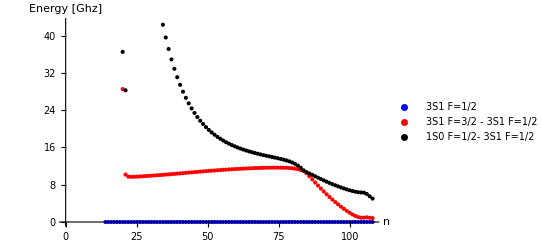

```mathematica
ListPlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2 - 3S1 F=1/2","1S0 F=1/2- 3S1 F=1/2"}],AxesLabel->{"
n","Energy [Ghz]"},DataRange->{14,Length[EnergyList3[[;;,1]]]+14}]
```

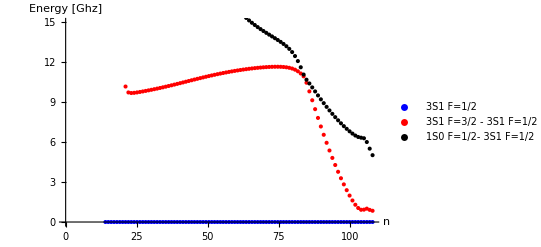

```mathematica
ListPlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2 - 3S1 F=1/2","1S0 F=1/2- 3S1 F=1/2"}],AxesLabel->{"
n","Energy [Ghz]"},DataRange->{14,Length[EnergyList3[[;;,1]]]+14},PlotRange->{0,15}]
```

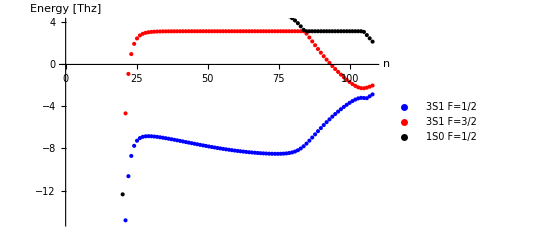

```mathematica
offset =15;
Split3s1Ip1 =EnergyList3[[;;,1]]-Table[Energy171[n,QuantumDefects ["μ's_3S1"]]1/cm^-1*29.979000*10^-3,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
Split3s1I1 =EnergyList3[[;;,2]]-Table[Energy171[n,QuantumDefects ["μ's_3S1"]]1/cm^-1*29.979000*10^-3,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
Split1s0I =EnergyList3[[;;,3]]-Table[Energy171[n,QuantumDefects ["μ's_3S1"]]1/cm^-1*29.979000*10^-3,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
ListPlot[{Split3s1Ip1 *10^3,Split3s1I1*10^3,Split1s0I*10^3},PlotStyle->{Blue,Red,Black},PlotLegends->LineLegend[{Blue,Red,Black},{"3S1 F=1/2","3S1 F=3/2","1S0 F=1/2"}],AxesLabel->{"
n","Energy [Thz]"},DataRange->{14,Length[EnergyList3[[;;,1]]]+14},PlotRange->{-15,4}]
```